```mathematica
Relu[x_]:=Piecewise[{{0,x<=0},{x,0<x<2},{2,x>=2}}]
```

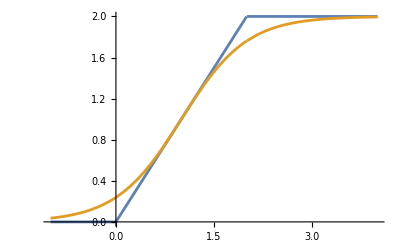

```mathematica
Plot[{Relu[x],2/(1+E^((-x+1)2))},{x,-1,4}]
```

-1

1.75

1

40

{{e1→InterpolatingFunction[…],e2→InterpolatingFunction[…]}}

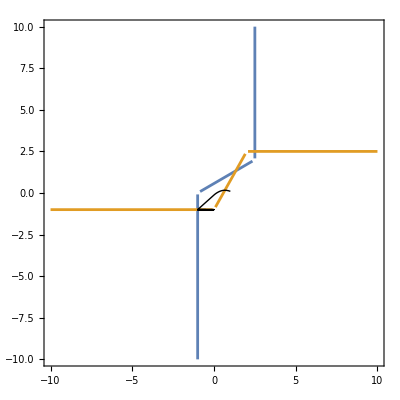

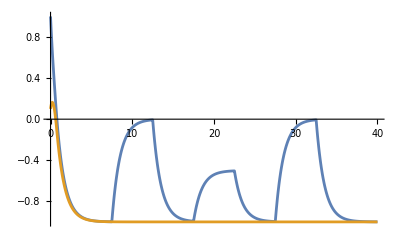

```mathematica
be =-1
gee = 1.75
s=1
time=40
sol2=NDSolve[{e1'[t]==-e1[t]+gee Relu[e2[t]]+be+s *in1[t][.5,5],e1[0]==1,e2'[t]==-e2[t]+gee Relu[e1[t]]+be,e2[0]==0.1},{e1,e2},{t,0,time}]

Show[
{ContourPlot[{e1==gee Relu[e2]+be,e2==gee Relu[e1]+be},{e1,-10,10},{e2,-10,10}],
ParametricPlot[{e1[t],e2[t]}/.sol2, {t,0,time},PlotStyle->{Thick,Black}]}]
Plot[{e1[t]/.sol2,e2[t]/.sol2},{t,0,time},PlotRange->All]
```

1

-1

0

0.5

{{e1→InterpolatingFunction[…],e2→InterpolatingFunction[…],i1→InterpolatingFunction[…],i2→InterpolatingFunction[…],o1→InterpolatingFunction[…]}}

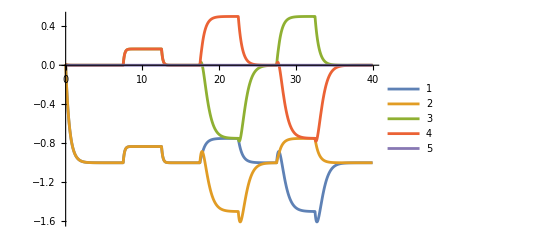

```mathematica
gee=2.;
gii =2.;
gei=2;1.75;
gie=2;1.75;
go=1
be=-1
bi =0
s=.5
time =40;
Relu[x_]:=Piecewise[{{0,x<=0},{x,0<x<2},{2,x>=2}}]




in1[t_][Δ_,dur_]:=HeavisidePi[(t-10)/dur] +Δ HeavisidePi[(t-20)/dur] + HeavisidePi[(t-30)/dur] 
in2[t_][Δ_,dur_]:=HeavisidePi[(t-10)/dur] + HeavisidePi[(t-20)/dur] +Δ HeavisidePi[(t-30)/dur] 
in1t[t_][Δ_,dur_]:=HeavisidePi[(t-10)/dur] + HeavisidePi[(t-Δ-20)/dur] + HeavisidePi[(t-30)/dur] 
in2t[t_][Δ_,dur_]:=HeavisidePi[(t-10)/dur] + HeavisidePi[(t-20)/dur] + HeavisidePi[(t-Δ-30)/dur] 
inph[t_][Δ_,per_]:=Sin[2π(t)/per-Δ]


sol4=NDSolve[{
.5e1'[t]==-e1[t]+gee Relu[e2[t]]-gie Relu[i1[t]] +be+s *in1[t][.5,5], e1[0]==0.01,
.5e2'[t]==-e2[t]+gee Relu[e1[t]]-gie Relu[i2[t]] +be+s*in2[t][.5,5], e2[0]==0.01,
.5i1'[t]==-i1[t]-gii Relu[i2[t]]+gei Relu[e2[t]] +bi+s*in1[t][.5,5], i1[0]==0.01,
.5i2'[t]==-i2[t]-gii Relu[i1[t]]+gei Relu[e1[t]] +bi+s*in2[t][.5,5], i2[0]==0.01,
.5o1'[t]==-o1[t]+go  (Relu[e1[t]]+Relu[e2[t]]),o1[0]==0
},{e1,e2,i1,i2,o1},{t,0,time},Method->"BDF"]
Plot[{e1[t]/.sol4,e2[t]/.sol4,i1[t]/.sol4,i2[t]/.sol4,o1[t]/.sol4},{t,0,time},PlotRange->All,PlotLegends->Automatic]
```

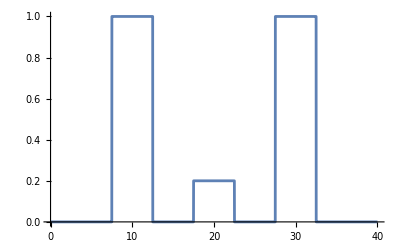

```mathematica
Plot[in1[t][.2,5],{t,0,time},Exclusions->None]
```

```mathematica
Monitor[dat=Table[
sol4=NDSolve[{
.5e1'[t]==-e1[t]+gee Relu[e2[t]]-gie Relu[i1[t]] +be+s *in1[t][.5,5], e1[0]==0.01,
.5e2'[t]==-e2[t]+gee Relu[e1[t]]-gie Relu[i2[t]] +be+s*in2[t][.5,5], e2[0]==0.01,
.5i1'[t]==-i1[t]-gii Relu[i2[t]]+gei Relu[e2[t]] +bi+s*in1[t][.5,5], i1[0]==.02,
.5i2'[t]==-i2[t]-gii Relu[i1[t]]+gei Relu[e1[t]] +bi+s*in2[t][.5,5], i2[0]==0.02,
.5o1'[t]==-o1[t]+go  (Relu[e1[t]]+Relu[e2[t]]),o1[0]==0
},{e1,e2,i1,i2,o1},{t,0,time},Method->"StiffnessSwitching"];
{o1[10]/.sol4[[1]],o1[20]/.sol4[[1]],o1[30]/.sol4[[1]],o1[40]/.sol4[[1]]},
{be,-2,2,.05},{bi,-4,5,.05}];,{be,bi}]


isGate[data_,thresh_]:=Block[{seg},
seg={If[data[[1]]>thresh,1,0],If[data[[2]]>thresh,1,0],If[data[[3]]>thresh,1,0],If[data[[4]]>thresh,1,0]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}}
}]
]
```

```mathematica
isGate[data_,thresh_]:=Block[{seg},
seg={If[data[[1]]>thresh,1,0],If[data[[2]]>thresh,1,0],If[data[[3]]>thresh,1,0],If[data[[4]]>thresh,1,0]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}}
},9]
]
```

```mathematica
`
```

1.5

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

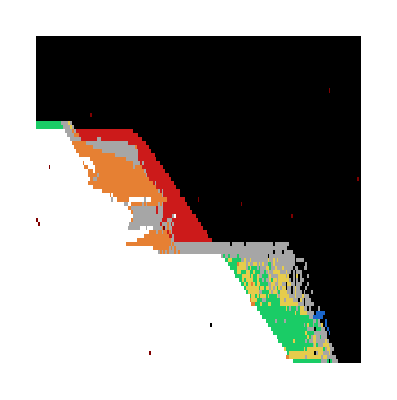

```mathematica
L[x_]:=Length[x]
thresh =1.5
logdat=Table[If[IntegerQ[isGate[dat[[i,j]],thresh]],isGate[dat[[i,j]],thresh],"Junk"],{i,1,L[dat]},{j,1,L[dat[[1]]]}];
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]

ArrayPlot[logdat,ColorRules->
{8->Black,1->White,4->red,2->orange,3->yellow,5->green,7->blue,6->purple,0->GrayLevel[grey],"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{-4,3},{-4,3}},Frame->Automatic,FrameLabel->{"Inhibitory Bias","Excitatory Bias"}(*PlotLabel->Style["Magnitude Logic","Title",Black,24]*)]
```

```mathematica
gee=2.;
gii =2;
gei=2;
gie=2;
go=1
s=.5
Δ=.5
Monitor[datT=Table[
sol4t=NDSolve[{
.5e1'[t]==-e1[t]+gee Relu[e2[t]]-gie Relu[i1[t]] +be+s *in1[t][Δ,5]+s *in1[t-50][Δ,5], e1[0]==0.01,
.5e2'[t]==-e2[t]+gee Relu[e1[t]]-gie Relu[i2[t]] +be+s*in2[t][Δ,5]+s *in1[t-50][Δ,5], e2[0]==0.01,
.5i1'[t]==-i1[t]-gii Relu[i2[t]]+gei Relu[e2[t]] +bi+s*in1[t][Δ,5]+s *in1[t-50][Δ,5], i1[0]==.02,
.5i2'[t]==-i2[t]-gii Relu[i1[t]]+gei Relu[e1[t]] +bi+s*in2[t][Δ,5]+s *in1[t-50][Δ,5], i2[0]==0.02,
.5o1'[t]==-o1[t]+go  (Relu[e1[t]]+Relu[e2[t]]),o1[0]==0
},{e1,e2,i1,i2,o1},{t,0,time},Method->"StiffnessSwitching"];
{o1[10]/.sol4t[[1]],o1[20]/.sol4t[[1]],o1[30]/.sol4t[[1]],o1[40]/.sol4t[[1]]},
{be,-2,2,.1},{bi,-4,5,.1}];,{be,bi}]
isGate[data_,thresh_]:=Block[{seg},
seg={If[data[[1]]>thresh,1,0],If[data[[2]]>thresh,1,0],If[data[[3]]>thresh,1,0],If[data[[4]]>thresh,1,0]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}}
},9]
]
```

1

0.5

0.5

NDSolve::smpf: Failure to project onto the discontinuity surface when computing Filippov continuation at time 7.09414.

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::smpf: Failure to project onto the discontinuity surface when computing Filippov continuation at time 7.13613.

NDSolve::smpf: Failure to project onto the discontinuity surface when computing Filippov continuation at time 0.00274229.

General::stop: Further output of NDSolve::smpf will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {10} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dprec: The precision of input value {20} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dprec: The precision of input value {30} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {80} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

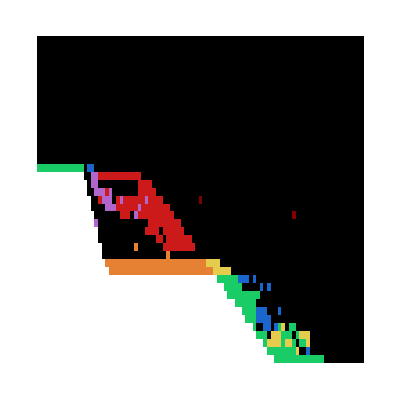

```mathematica
L[x_]:=Length[x]
thresh=3
logdat=Table[If[IntegerQ[isGate[datT[[i,j]],thresh]],isGate[datT[[i,j]],thresh],"Junk"],{i,1,L[datT]},{j,1,L[datT[[1]]]}];
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]

ArrayPlot[logdat,ColorRules->
{8->Black,1->White,4->red,2->orange,3->yellow,5->green,7->blue,6->purple,0->GrayLevel[grey],"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{-4,4},{-2,2}},FrameTicks->True,Frame->Automatic,AspectRatio->1,FrameLabel->{"Inhibitory Bias","Excitatory Bias"}(*PlotLabel->Style["Magnitude Logic","Title",Black,24]*)]
```

```mathematica
s
```

1

```mathematica
logdat=Table[If[IntegerQ[isGate[datT[[i,j]],2]],isGate[datT[[i,j]],2],9],{i,1,L[datT]},{j,1,L[datT[[1]]]}];
```

```mathematica
logdat[[7]]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
74/16./18.
```

0.256944

```mathematica
gee=2.;
gii =2;
gei=2;
gie=2;
go=1
s=1
Δ1=.0
Δ2=0
per =15
time =60
bem = -2
bep = 6
dele = .1
bim =-2
bip = 10
deli =.1
Monitor[datSyn=Table[
solSyn=NDSolve[{
.5e1'[t]==-e1[t]+gee Relu[e2[t]]-gie Relu[i1[t]] +be+s *inph[t][Δ1,per], e1[0]==0.01,
.5e2'[t]==-e2[t]+gee Relu[e1[t]]-gie Relu[i2[t]] +be+s*inph[t][Δ2,per], e2[0]==0.01,
.5i1'[t]==-i1[t]-gii Relu[i2[t]]+gei Relu[e2[t]] +bi+s*inph[t][Δ1,per], i1[0]==.02,
.5i2'[t]==-i2[t]-gii Relu[i1[t]]+gei Relu[e1[t]] +bi+s*inph[t][Δ2,per], i2[0]==0.02,
.5o1'[t]==-o1[t]+go  (Relu[e1[t]]+Relu[e2[t]]),o1[0]==0
},{e1,e2,i1,i2,o1},{t,0,time},Method->"StiffnessSwitching"];
Table[o1[t]/.solSyn,{t,20,time,.1}],
{be,bem,bep,dele},{bi,bim,bip,deli}];,{be,bi}]

Δ1=π
Δ2=0
Monitor[datASyn=Table[
solASyn=NDSolve[{
.5e1'[t]==-e1[t]+gee Relu[e2[t]]-gie Relu[i1[t]] +be+s *inph[t][Δ1,per], e1[0]==0.01,
.5e2'[t]==-e2[t]+gee Relu[e1[t]]-gie Relu[i2[t]] +be+s*inph[t][Δ2,per], e2[0]==0.01,
.5i1'[t]==-i1[t]-gii Relu[i2[t]]+gei Relu[e2[t]] +bi+s*inph[t][Δ1,per], i1[0]==.02,
.5i2'[t]==-i2[t]-gii Relu[i1[t]]+gei Relu[e1[t]] +bi+s*inph[t][Δ2,per], i2[0]==0.02,
.5o1'[t]==-o1[t]+go  (Relu[e1[t]]+Relu[e2[t]]),o1[0]==0
},{e1,e2,i1,i2,o1},{t,0,time},Method->"StiffnessSwitching"];
Table[o1[t]/.solASyn,{t,20,time,.1}],
{be,bem,bep,dele},{bi,bim,bip,deli}];,{be,bi}]

Δ1=.3π
Δ2=0
Monitor[datAdv=Table[
solAdv=NDSolve[{
.5e1'[t]==-e1[t]+gee Relu[e2[t]]-gie Relu[i1[t]] +be+s *inph[t][Δ1,per], e1[0]==0.01,
.5e2'[t]==-e2[t]+gee Relu[e1[t]]-gie Relu[i2[t]] +be+s*inph[t][Δ2,per], e2[0]==0.01,
.5i1'[t]==-i1[t]-gii Relu[i2[t]]+gei Relu[e2[t]] +bi+s*inph[t][Δ1,per], i1[0]==.02,
.5i2'[t]==-i2[t]-gii Relu[i1[t]]+gei Relu[e1[t]] +bi+s*inph[t][Δ2,per], i2[0]==0.02,
.5o1'[t]==-o1[t]+go  (Relu[e1[t]]+Relu[e2[t]]),o1[0]==0
},{e1,e2,i1,i2,o1},{t,0,time},Method->"StiffnessSwitching"];
Table[o1[t]/.solAdv,{t,20,time,.1}],
{be,bem,bep,dele},{bi,bim,bip,deli}];,{be,bi}]



Δ1=-.3π
Δ2=0
Monitor[datDel=Table[
solDel=NDSolve[{
.5e1'[t]==-e1[t]+gee Relu[e2[t]]-gie Relu[i1[t]] +be+s *inph[t][Δ1,per], e1[0]==0.01,
.5e2'[t]==-e2[t]+gee Relu[e1[t]]-gie Relu[i2[t]] +be+s*inph[t][Δ2,per], e2[0]==0.01,
.5i1'[t]==-i1[t]-gii Relu[i2[t]]+gei Relu[e2[t]] +bi+s*inph[t][Δ1,per], i1[0]==.02,
.5i2'[t]==-i2[t]-gii Relu[i1[t]]+gei Relu[e1[t]] +bi+s*inph[t][Δ2,per], i2[0]==0.02,
.5o1'[t]==-o1[t]+go  (Relu[e1[t]]+Relu[e2[t]]),o1[0]==0
},{e1,e2,i1,i2,o1},{t,0,time},Method->"StiffnessSwitching"];
Table[o1[t]/.solDel,{t,20,time,.1}],
{be,bem,bep,dele},{bi,bim,bip,deli}];,{be,bi}]
```

1

1

0.

0

15

60

-2

6

0.1

-2

10

0.1

NDSolve::smpf: Failure to project onto the discontinuity surface when computing Filippov continuation at time 15.2485.

InterpolatingFunction::dmval: Input value {20.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::smpf: Failure to project onto the discontinuity surface when computing Filippov continuation at time 0.00268008.

NDSolve::smpf: Failure to project onto the discontinuity surface when computing Filippov continuation at time 0.0397608.

General::stop: Further output of NDSolve::smpf will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {20.2} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dprec: The precision of input value {20.3} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dprec: The precision of input value {20.7} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

π

0

0.942478

0

-0.942478

0

1

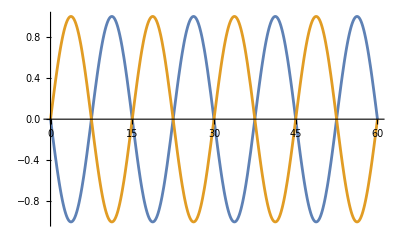

```mathematica
isGatePh[dataSynch_,dataDelay_,dataAsynch_,datAdv_ ,thresh_]:=Block[{seg},
seg={If[Max[dataSynch]>thresh,1,0,-1],If[Max[dataDelay]>thresh,1,0,-1],If[Max[datAdv]>thresh,1,0,-1],If[Max[dataAsynch]>thresh,1,0,-1]};
Piecewise[{
{1,seg=={1,1,1,1}},
{2,seg=={1,1,1,0}},
{3,seg=={0,1,1,0}},
{4,seg=={1,0,0,0}},
{5,seg=={0,1,1,1}},
{6,seg=={1,0,0,1}},
{7,seg=={0,0,0,1}},
{8,seg=={0,0,0,0}}
}]
]
trans = 1
dat=Table[isGatePh[datSyn[[i,j,trans;;-1]],datDel[[i,j,trans;;-1]],datASyn[[i,j,trans;;-1]],datDel[[i,j,trans;;-1]],1.7],{i,1,Length[datAdv]},{j,1,Length[datAdv[[1]]]}];
```

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

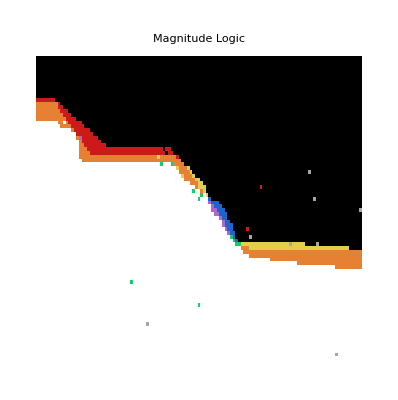

```mathematica
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]

ArrayPlot[dat,ColorRules->
{8->Black,1->White,4->red,2->orange,3->yellow,5->green,7->blue,6->purple,0->GrayLevel[grey],"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{1.5,4.5},{-2.5,0.5}},FrameTicks->Automatic,FrameLabel->{"Inhibitory Bias","Excitatory Bias"},PlotLabel->Style["Magnitude Logic","Title",Black,24]]
```